```mathematica
(*~~ 1. Basic model trajectory ~~*)
DiffSystem1={
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
(*Trajectory plot*)
DiffNDSol = NDSolve[{DiffSystem1/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 0, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]->0, Subscript[γ, H]-> 0}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.DiffNDSol[[1,1]]], Evaluate[y[t]/.DiffNDSol[[1,2]]], Evaluate[w[t]/.DiffNDSol[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,0.72}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
(*~~ 2. 3D plots {"β_AH","Λ_A", "R_H^*"} ~~*)
(*Plotting functions*)
EqSystem1 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
NSolSys1[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{EqSystem1[[1]]==0, EqSystem1[[2]]==0, EqSystem1[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals]
plot1env[bha_, bah_,LA_] := Evaluate[NSolSys1[1/10, LA, 1/10, 1/10, 1/10, 1/10, bah, 1/100, bha, 1/10, 1/10, 1/10, 1/10, 1/10, 1/5]][[1,1,2]]
plot1noenv[bha_, bah_,LA_] := Evaluate[NSolSys1[1/10, LA, 0, 0, 1/10, 1/10, bah, 0, bha, 0, 0, 0, 1/10, 1/10, 0]][[1,1,2]]
```

```mathematica
(*With environment, high impact*)
Plot3D[plot1env[1/10, par1, par2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}]
```

-Graphics3D-

```mathematica
(*No environment, high impact*)
Plot3D[plot1noenv[1/10, par1, par2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*~~ 2. Solve ~~*)
(* Step 1. Use equations for RE and RA, assuming steady RH *)
ODESystem3 = {
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x - Subscript[μ, e]*w[t]
};
```

```mathematica
(* Step 2. Solve this system for equilibrium *)
sol2 = DSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0}, {y,w},t, 
Assumptions->{Subscript[β, HA]≥ 0, Subscript[β, AA]≥ 0, Subscript[β, EA]≥ 0, Subscript[β, AE]≥ 0,Subscript[β, HE]≥ 0, Subscript[μ, e]≥ 0, Subscript[μ, A]≥ 0, x≥ 0, Subscript[γ, A]≥ 0, Subscript[γ, H]≥ 0, Subscript[Λ, A]≥ 0, Subscript[Λ, H]≥ 0}];
```

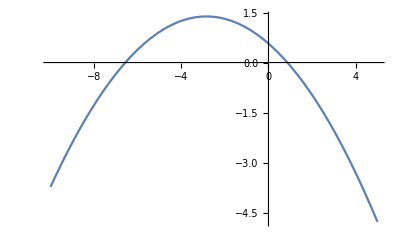

```mathematica
(*This gives us two solutions, with equations of quadratic form. We need to select the 'positive' solution.*)
(*Demonstrate for self satisfaction that we are working with quadratic functions *)
f[y_] := (1-y) * (0.1+0.1*0.7+0.1*y + 0.2 * 2)-0.1*y
Plot[f[w], {w, -10, 5}]
```

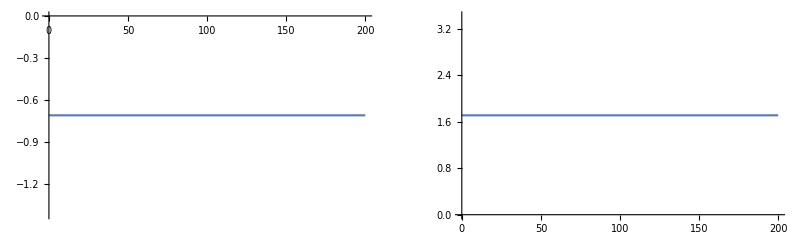

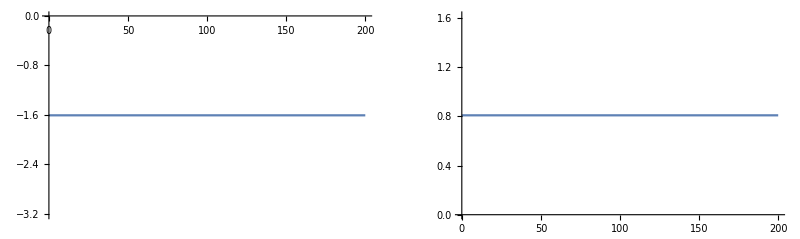

```mathematica
(* Step 3. Select correct solution. Have to plot the different solutions to look at what value they are suggesting*)
solv1 = sol2[[1]]; (*RA==0*)
solv2 = sol2[[2]]; (*RE==0*)
wv1 = Plot[Evaluate[w[t]/.solv1[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
wv2 = Plot[Evaluate[w[t]/.solv2[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{wv1, wv2}]
yv1 = Plot[Evaluate[y[t]/.solv1[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
yv2 = Plot[Evaluate[y[t]/.solv2[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{yv1, yv2}]
(*Solution two is the (biologically speaking) right solution. Now Try to simplify.*)
```

```mathematica
(*Simplify to get a simpler equation*)
yorigeq = solv2[[2, 2, 2]]; (*eq found above*)
yeq= FullSimplify[yorigeq]; (*can we get a simper one?*)
```

```mathematica
worigeq = solv2[[1, 2, 2]];
weq = FullSimplify[worigeq];
```

```mathematica
(*Looking at plots with RH on one axis and RA or RE on the other, and looking at conseqence of different parameter combinations.*)
(*Define functions so that we can make plots*)
yfunc[xs_, bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_ ] := yeq /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
wfunc[xs_,bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_]:= weq/.{Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1,Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
```

```mathematica
(*Can use a manipulate plot - but not on an i5*) (*Manipulate[Plot[{yfunc[par1, bea, bhe, bae, mue, Le], wfunc[par1, bea, bhe, bae, mue, Le]},{par1,0,1}, AxesLabel->{"R_H^*", "R^*"}, PlotRange->{{0,1},{0,3}}], {bea, 0, 1}, {bhe, 0, 1},{bae, 0, 1}, {mue, 0, 1.0}, {Le, 0, 0.1}]*)
```

```mathematica
(* Step 4. Solve analytical solutions for x*)
yeqx = Solve[yeq==y, x];(*x on right hand side*)
ytargfixedx= Solve[0.7 == yeqx[[1,1,2]], y]; (*for a given x, what par combinations/RA values are possible?*)
ytargfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1} (*find right solution*)
```

{{y→-2.21816},{y→0.723106}}⟦i,1,2⟧

```mathematica
yfixedxplot[La_, bHE_] :=Evaluate[ytargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[yfixedxplot[par1,par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

-Graphics3D-

```mathematica
weqx = Solve[{w == weq}, x];
weqx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1, w -> 2} (*which solution is positive?*)
```

{{x→16.7507},{x→-222.051}}⟦i,1,2⟧

```mathematica
wtargfixedx = Solve[0.7==weqx[[1,1,2]], w];
(*which solution is the right one*) 
wtargfixedx[[i,1,2]]/.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}
```

{{w→-1.03418},{w→0.954183}}⟦i,1,2⟧

```mathematica
wfixedxplot[La_, bHE_] :=Evaluate[wtargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[wfixedxplot[par1, par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

-Graphics3D-

```mathematica
(*Equilibrium analysis for sensitivity analysis*)
ODESystem3 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
equilibrium[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0, ODESystem3[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
parameters = Rest[Import["M:\\New projects\\Model env compartment\\paramodel.csv"]];
```

{{1,0.996401,0.992257,0.00982318,0.986369,0.983315,0.0176817,0.979826,0.977749,0.9759,0.0251963,0.0263904,0.973477,0.0271597,0.027699,0.0275059},9169,{9171,0.00359869,0.00774264,0.990177,0.0136314,0.0166848,0.982318,0.0201745,0.0222513,0.0241003,0.974804,0.97361,0.0265226,0.97284,0.972301,0.972495}}
 |  |  |  |

```mathematica
eqanalysis = Table[equilibrium[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Dimensions[eqanalysis]
```

{9171}

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibrium.csv", eqanalysis];
```